```mathematica
Needs["Quantum`Notation`"]
```

Quantum`Notation` 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.
Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

MATHEMATICA 12.1.1 for Microsoft Windows (64-bit) (June 19, 2020)

QUANTUM version EN CONSTRUCCION

TODAY IS Mon 16 Nov 2020 00:50:37

```mathematica
SetQuantumAliases[];
```

```mathematica
ClearAliases[]
```

## Number of Flavors

```mathematica
M=8;
```

## Define fermionic operators

```mathematica
⟨Subscript[j_, OverHat[α_]]|·|Subscript[k_, OverHat[β_]]⟩:=KroneckerDelta[j-k]KroneckerDelta[α-β]
Table[DefineOperatorOnKets[Subscript[a, α̂],{|Subscript[n_, α̂]⟩:>Boole[n==1]|Subscript[0, α̂]⟩}],{α, 1, M}]
Table[DefineOperatorOnKets[SuperDagger[(Subscript[a, α̂])],{|Subscript[n_, α̂]⟩:>Boole[n==0]|Subscript[1, α̂]⟩}],{α, 1, M}]
⟦Subscript[a, OverHat[α_]],SuperDagger[(Subscript[a, OverHat[β_]])]⟧_+:=KroneckerDelta[α-β]; Subscript[a, OverHat[α_]]^2:=0 ;SuperDagger[(Subscript[a, OverHat[α_]])]^2:=0;
```

{|n__OverHat[1]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[2]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[3]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[4]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[5]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[6]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[7]⟩:>Boole[n==1] |0_(α̂)⟩,|n__OverHat[8]⟩:>Boole[n==1] |0_(α̂)⟩}

{|n__OverHat[1]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[2]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[3]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[4]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[5]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[6]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[7]⟩:>Boole[n==0] |1_(α̂)⟩,|n__OverHat[8]⟩:>Boole[n==0] |1_(α̂)⟩}

```mathematica
Subscript[a, OverHat[1]]·|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩
Subscript[a, OverHat[2]]·|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩
SuperDagger[(Subscript[a, OverHat[1]])]^2·|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩
Subscript[a, OverHat[2]]·|Subscript[0, OverHat[2]]⟩
SuperDagger[(Subscript[a, OverHat[2]])]·|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩
Subscript[a, OverHat[2]]^2·|Subscript[1, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩
SuperDagger[(Subscript[a, OverHat[2]])]^2·|Subscript[0, OverHat[1]]⟩⊗|Subscript[0, OverHat[2]]⟩
SuperDagger[(Subscript[a, OverHat[2]])]·Subscript[a, OverHat[2]]·|Subscript[0, OverHat[1]]⟩⊗|Subscript[1, OverHat[2]]⟩
SuperDagger[(Subscript[a, OverHat[2]])]·Subscript[a, OverHat[2]]·|Subscript[1, OverHat[2]]⟩
```

|0_OverHat[1],1_OverHat[2]⟩

|1_OverHat[1],0_OverHat[2]⟩

0

0

|0_OverHat[1],1_OverHat[2]⟩

0

0

|0_OverHat[1],1_OverHat[2]⟩

|1_OverHat[2]⟩

## Hamiltonian for U(1)

where

For U(N=1), no color index is considered, and Tr runs over the flavor indices.

```mathematica
H[γ_, β_, M_] :=    β Sum[SuperDagger[(Subscript[a, î])]·Subscript[a, î], {i, 1, M}]+γ Sum[SuperDagger[(Subscript[a, î])]·Subscript[a, î]·SuperDagger[(Subscript[a, ĵ])]·Subscript[a, ĵ], {i, 1, M}, {j, 1, M}]
```

## Fock States

```mathematica
IntegerDigitsFixed[n_, d_, l_]:=Table[If[i >= l-Length[IntegerDigits[n, d]]+1, IntegerDigits[n, d][[i-(l-Length[IntegerDigits[n, d]])]], 0], {i, 1, l}]
FockStates =Table[⊗_(α=1)^M(SuperDagger[(Subscript[a, α̂])]^IntegerDigitsFixed[n, 2, M][[M-α+1]]·|Subscript[0, α̂]⟩), {n, 0, 2^M-1}];
```

## Create singlets with fixed particle number

```mathematica
Singlets = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, FockStates[[n+1]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
```

```mathematica
Hmat[i_, j_, γ_, β_, M_]:=SuperDagger[(Singlets[[i]])]·H[γ, β, M]·Singlets[[j]]
```

## Compute Spectrum

{0.,2.,6.,12.,20.,30.,42.,56.,72.}

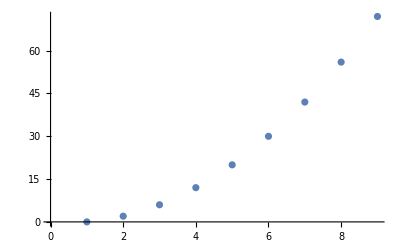

```mathematica
Spec=Table[Hmat[i, i, 1, 1, M], {i, 1, M+1}]//N
ListPlot[Spec]
```

## Comparison to the Exact Spectrum in the Flux Basis

```mathematica
Llist[g_,L_] := Table [- g^2/2,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[ 3m^2/2   +  g^2,{m,-L, L }] ]
```

```mathematica
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
MatrixForm[FluxPlaqOperator[1,4]//N]
```

(25. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.5 | 14.5 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 7. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 2.5 | -0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 1. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.5 | 2.5 | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 7. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 14.5 | -0.5
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 25.)

```mathematica
Sort[Eigenvalues[FluxPlaqOperator[0.1,128]//N]//N, Less][[1;;10]]
```

{0.00996667,1.50999,1.51003,6.01,6.01,13.51,13.51,24.01,24.01,37.51}

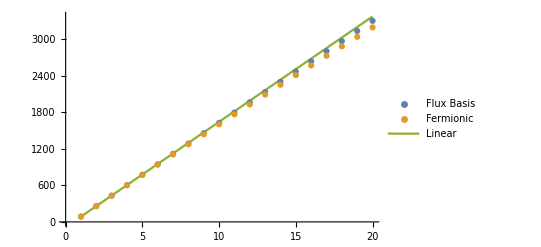

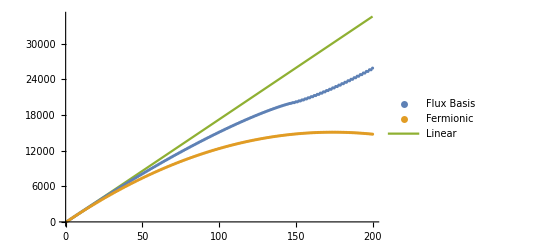

```mathematica
g =100;
Eigvalues=Sort[Eigenvalues[FluxPlaqOperator[g, 256]//N]//N, Less];
ListPlot[{Eigvalues[[1;;20]],Table[Sqrt[3]g m-1/2m^2 + Sqrt[3]g/2  , {m, 0, 19}], Table[Sqrt[3]g m + Sqrt[3]g/2, {m, 0, 19}]}, PlotLegends->{"Flux Basis", "Fermionic", "Linear"}, Joined->{False, False, True}]
ListPlot[{Eigvalues[[1;;200]],Table[Sqrt[3]g m-1/2m^2 + Sqrt[3]g/2  , {m, 0, 199}], Table[Sqrt[3]g m + Sqrt[3]g/2, {m, 0, 199}]}, PlotLegends->{"Flux Basis", "Fermionic", "Linear"}, Joined->{False, False, True}]
```

```mathematica
Fit[Sort[Eigenvalues[FluxPlaqOperator[g, 256]//N]//N, Less][[1;;100]], {1,x, x ^2}, x]
```

-106.618+175.547 x-0.233563 x^2

## Need to find out why but the factor 1/2 of the quadratic term does not work well but another ~1/4.5 does

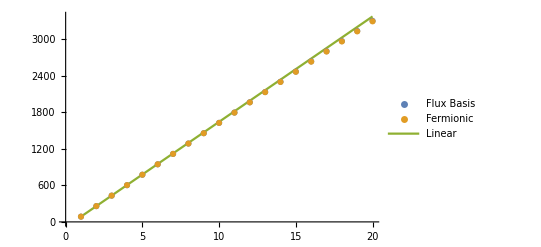

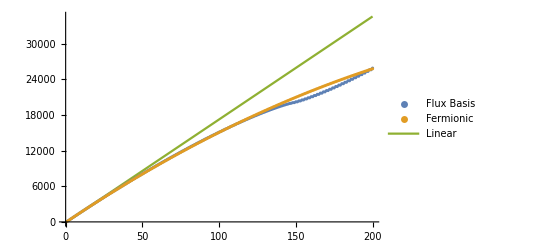

```mathematica
ListPlot[{Eigvalues[[1;;20]],Table[Sqrt[3]g m-m^2/4.5 + Sqrt[3]g/2  , {m, 0, 19}], Table[Sqrt[3]g m + Sqrt[3]g/2, {m, 0, 19}]}, PlotLegends->{"Flux Basis", "Fermionic", "Linear"}, Joined->{False, False, True}]
ListPlot[{Eigvalues[[1;;200]],Table[Sqrt[3]g m-m^2/4.5 + Sqrt[3]g/2  , {m, 0, 199}], Table[Sqrt[3]g m + Sqrt[3]g/2, {m, 0, 199}]}, PlotLegends->{"Flux Basis", "Fermionic", "Linear"}, Joined->{False, False, True}]
```